```mathematica
energiesAt[Ef_, M_] := Eigensystem[M /. {ΔE -> Ef}][[1]]
energiesInOrder[Ef_, M_] := energiesAt[Ef, M][[order[Ef, M]]]
statesAt[Ef_, M_] := Eigensystem[M /. {ΔE -> Ef}][[2]]
statesInOrder[Ef_, M_] := statesAt[Ef, M][[order[Ef, M]]]

targetStates = IdentityMatrix[8];
order[Ef_, M_] := Table[Ordering[row, -1][[1]], {row,Abs[targetStates.ConjugateTranspose[statesAt[Ef, M]]]}]
putInOrder[Q_, Ef_, M_] := Q[[order[Ef, M]]]
```

```mathematica
HrotatingJ = HnsInGE;
HstaticJ = H;

Eff = Diagonal[H][[3]] - Diagonal[H][[2]];
EeSpin = Diagonal[H][[3]] - Diagonal[H][[1]];
EnSpin = Diagonal[H][[1]] - Diagonal[H][[2]];
ϵ0;

setVariables[]
ΔE = 0;
Bac = .001;
Eac = .001;
B0 = B0*1.0056;

δB = 10^7;

νB = EeSpin - δB;
νE = Eff - δB;
δE = ϵ0 - νE;

{Eff, EeSpin, EnSpin, ϵ0}

printWithBasis[2*π*H, basisGE]

Bac = 0;
Eac = 0;
t = 0;
energiesInOrder[0, 2*π*H] // MatrixForm
statesInOrder[0, 2*π*H] // MatrixForm


clearVariables[]
```

{5.62317×10^9,5.59045×10^9,3.27153×10^7,5.62325×10^9}

( | |g↓⇓> | |g↓⇑> | |g↑⇓> | |g↑⇑> | |e↓⇓> | |e↓⇑> | |e↑⇓> | |e↑⇑>
|g↓⇓> | -3.5218×10^10 | 0. | 0. | 0 | 1.09553×10^8 | 0 | 0 | 0
|g↓⇑> | 0. | -3.54236×10^10 | 1.83783×10^8 | 0. | 0 | -7.42305×10^7 | 1.83783×10^8 | 0
|g↑⇓> | 0. | 1.83783×10^8 | -9.21543×10^7 | 0. | 0 | 1.83783×10^8 | -1.09575×10^8 | 0
|g↑⇑> | 0 | 0. | 0. | 6.98558×10^7 | 0 | 0 | 0 | 7.42077×10^7
|e↓⇓> | 1.09553×10^8 | 0 | 0 | 0 | 1.13927×10^8 | 0. | 0. | 0
|e↓⇑> | 0 | -7.42305×10^7 | 1.83783×10^8 | 0 | 0. | -9.16289×10^7 | 1.83783×10^8 | 0.
|e↑⇓> | 0 | 1.83783×10^8 | -1.09575×10^8 | 0 | 0. | 1.83783×10^8 | 3.52398×10^10 | 0.
|e↑⇑> | 0 | 0 | 0 | 7.42077×10^7 | 0 | 0. | 0. | 3.54018×10^10)

(-3.52183×10^10
-3.54251×10^10
9.19816×10^7
6.96998×10^7
1.14267×10^8
-2.75929×10^8
3.52415×10^10
3.54019×10^10)

(0.999995 | 5.51817×10^-19 | 1.96077×10^-19 | 0. | -0.00310095 | 0. | -1.48198×10^-19 | 0.
4.71868×10^-19 | -0.999981 | 0.0052206 | 0. | 0. | -0.00214124 | 0.00261438 | 0.
-2.74788×10^-19 | 0.00217986 | 0.707961 | 0. | 0. | 0.706247 | -0.00149739 | 0.
0. | 0. | 0. | -0.999998 | 0. | 0. | 0. | 0.00210061
-0.00310095 | 9.06932×10^-17 | -7.35209×10^-17 | 0. | -0.999995 | 0. | -7.35204×10^-17 | 0.
2.7413×10^-19 | -0.00521811 | -0.706226 | 0. | 0. | 0.707943 | -0.00581506 | 0.
-1.95052×10^-19 | -0.00258731 | 0.00306037 | 0. | 0. | -0.00517997 | -0.999979 | 0.
0. | 0. | 0. | 0.00210061 | 0. | 0. | 0. | 0.999998)

0.160896

{ψ[1][t],ψ[2][t],ψ[3][t],ψ[4][t],ψ[5][t],ψ[6][t],ψ[7][t],ψ[8][t]}

{-3.16892×10^10 ψ[1][t]-37890.7 Sin[2.79347×10^10 t] ψ[2][t]+6.15092×10^7 Sin[2.79347×10^10 t] ψ[3][t]+2 π (1.68751×10^7-3.62698×10^8 Cos[2.81375×10^10 t]) ψ[5][t]==ⅈ ψ[1]'[t],-37890.7 Sin[2.79347×10^10 t] ψ[1][t]-3.18904×10^10 ψ[2][t]+1.83783×10^8 ψ[3][t]+6.15092×10^7 Sin[2.79347×10^10 t] ψ[4][t]+2 π (-1.23749×10^7-3.62698×10^8 Cos[2.81375×10^10 t]) ψ[6][t]+1.83783×10^8 ψ[7][t]==ⅈ ψ[2]'[t],6.15092×10^7 Sin[2.79347×10^10 t] ψ[1][t]+1.83783×10^8 ψ[2][t]-3.62529×10^9 ψ[3][t]-37890.7 Sin[2.79347×10^10 t] ψ[4][t]+1.83783×10^8 ψ[6][t]+2 π (-1.68751×10^7-3.62698×10^8 Cos[2.81375×10^10 t]) ψ[7][t]==ⅈ ψ[3]'[t],6.15092×10^7 Sin[2.79347×10^10 t] ψ[2][t]-37890.7 Sin[2.79347×10^10 t] ψ[3][t]-3.45893×10^9 ψ[4][t]+2 π (1.23749×10^7-3.62698×10^8 Cos[2.81375×10^10 t]) ψ[8][t]==ⅈ ψ[4]'[t],2 π (1.68751×10^7-3.62698×10^8 Cos[2.81375×10^10 t]) ψ[1][t]+3.64271×10^9 ψ[5][t]-37890.7 Sin[2.79347×10^10 t] ψ[6][t]+6.15092×10^7 Sin[2.79347×10^10 t] ψ[7][t]==ⅈ ψ[5]'[t],2 π (-1.23749×10^7-3.62698×10^8 Cos[2.81375×10^10 t]) ψ[2][t]+1.83783×10^8 ψ[3][t]-37890.7 Sin[2.79347×10^10 t] ψ[5][t]+3.44151×10^9 ψ[6][t]+1.83783×10^8 ψ[7][t]+6.15092×10^7 Sin[2.79347×10^10 t] ψ[8][t]==ⅈ ψ[6]'[t],1.83783×10^8 ψ[2][t]+2 π (-1.68751×10^7-3.62698×10^8 Cos[2.81375×10^10 t]) ψ[3][t]+6.15092×10^7 Sin[2.79347×10^10 t] ψ[5][t]+1.83783×10^8 ψ[6][t]+3.17066×10^10 ψ[7][t]-37890.7 Sin[2.79347×10^10 t] ψ[8][t]==ⅈ ψ[7]'[t],2 π (1.23749×10^7-3.62698×10^8 Cos[2.81375×10^10 t]) ψ[4][t]+6.15092×10^7 Sin[2.79347×10^10 t] ψ[6][t]-37890.7 Sin[2.79347×10^10 t] ψ[7][t]+3.1873×10^10 ψ[8][t]==ⅈ ψ[8]'[t],ψ[1][0]==0.999995,ψ[2][0]==1.64501×10^-18,ψ[3][0]==3.33254×10^-19,ψ[4][0]==0.,ψ[5][0]==-0.00300092,ψ[6][0]==0.,ψ[7][0]==8.52947×10^-23,ψ[8][0]==0.}

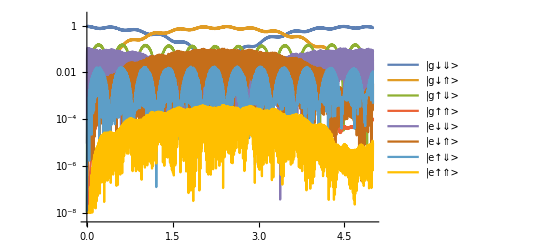

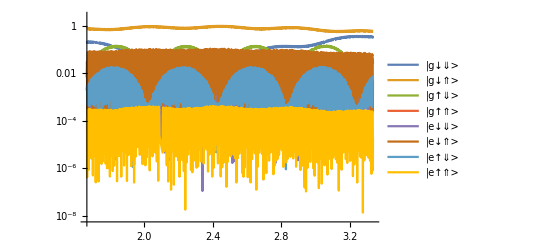

```mathematica
setVariables[]
ΔE = 0;
A = A0;
B0 = .8*B0*1.0056;
B0

Bac = 0;
Eac = 0;
Eff = (energiesInOrder[0, H][[3]] - energiesInOrder[0, H][[2]]);
EeSpin = (energiesInOrder[0, H][[3]] - energiesInOrder[0, H][[1]]);
undrivenStates = statesInOrder[0, H];
Bac = .0007;
Eac = 200;

δB = 2*10^7;

νB = EeSpin - δB;
νE = (Eff - δB);
(*νE = ϵ0;*)

δE = (ϵ0 - νE);

M = 2*π*H;

(*printWithBasis[M - IdentityMatrix[8]*Diagonal[M][[3]], basisGE]*)

(*ψ0 = {1, 0, 0, 0, 0, 0, 0, 0};*)
ψ0 = undrivenStates[[1]];

Tmax = 500*10^-9;

funcs=Array[ψ[#1][t]&,{Length[ψ0]}]
equations=Flatten@Join[Thread[M.funcs == ⅈ*D[funcs,t]],Thread[funcs==ψ0/.t->0]]

state= NDSolveValue[equations,funcs,{t,0,Tmax}];
state = Abs[state]^2;
LogPlot[Evaluate@Table[Max[state[[i]], 10^-8], {i, Length[state]}],{t,0,Tmax}, PlotRange->All, PlotLegends->basisGE]
LogPlot[Evaluate@Table[Max[state[[i]], 10^-8], {i, Length[state]}],{t,Tmax/3,2*Tmax/3}, PlotRange->All, PlotLegends->basisGE]

clearVariables[];
```